```mathematica
pt = RandomPoint[Ball[ConstantArray[0,50]],1000];
```

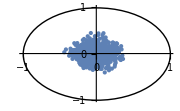

~/papers/dl-stats/paper/fig/hd_ball.pdf

```mathematica
data=Transpose@{pt[[All,1]],pt[[All,2]]};
p1 = ListPlot[data, PlotStyle->PointSize[Small]];
p2 = Graphics[Circle[{0,0},1]];
pc = Show[p1,p2, PlotRange->All, AxesStyle->Black, ImageSize->Small]
Export["~/papers/dl-stats/paper/fig/hd_ball.pdf", pc]
```

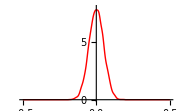

~/papers/dl-stats/paper/fig/hd_hist_400.pdf

```mathematica
pt = RandomPoint[Ball[ConstantArray[0,400]],5000];
sh = SmoothHistogram[Style[pt[[All,1]], Thick, Red],PlotRange->{{-0.5,0.5},{0,8}},AxesStyle->Black, ImageSize->Small]
Export["~/papers/dl-stats/paper/fig/hd_hist_400.pdf", sh]
```

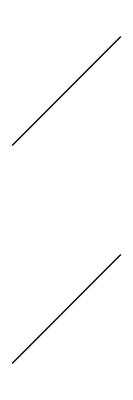

```mathematica
Graphics[{ Line[{{1,0},{2,1}}],Line[{{2,3},{1,2}}]}]
```

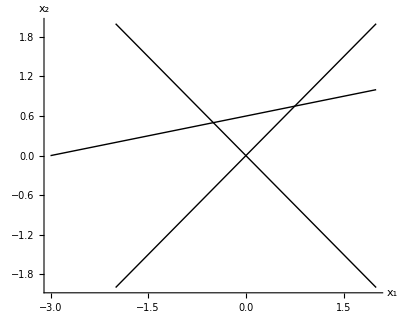

```mathematica
Graphics[{ Line[{{-3,0},{2,1}}],Line[{{-2,2},{2,-2}}], Line[{{-2,-2},{2,2}}]}, Axes->True, AxesLabel->{Subscript[x, 1],Subscript[x, 2]}, AxesStyle->Blac]
```

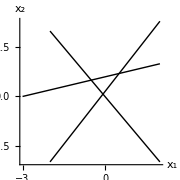

```mathematica
Show[Graphics[{Line[{{-3,0},{2,1}}],Line[{{-2,2},{2,-2}}],Line[{{-2,-2},{2,2.3}}]},Axes->True,AxesLabel->{Subscript[x, 1],Subscript[x, 2]},AxesStyle->GrayLevel[0],AxesStyle->Thickness[Large]],ImageSize->Small]
```